## Sign error in Linkwitz-Riley second order crossover filters

We plot the transfer function of the second order Linkwitz-Riley lowpass filter with cutoff at 0.5 radians:

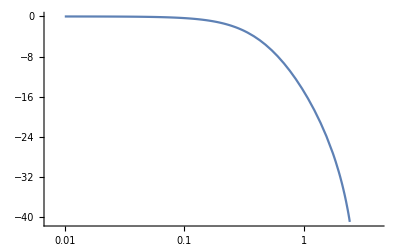

```mathematica
(* some helper functions *)
γ[fc_]:=Tan[fc/2] (* fc in radians*)
zz[ω_]:=ⅇ^(ⅈ ω) (* convert ω in radians to complex number z *)
linearToDb[linear_]:=20Log10[linear]

(* a0, a1, a2. Note a0 will be normalised to 1 so all others are divided by a0 *)
a0lp[γ_]:=γ^2+2 γ+1
a1lp[γ_]:=2 (γ^2-1)/a0lp[γ]
a2lp[γ_]:=(γ^2-2 γ+1)/a0lp[γ]

(* b0, b1, b2 *)
b0lp[γ_]:=γ^2/a0lp[γ]
b1lp[γ_]:=2 b0lp[γ]
b2lp[γ_]:=b0lp[γ]
         
(* lowpass transfer function *)
lwLp[z_,fc_]:=(b0lp[γ[fc]] + b1lp[γ[fc]]z^(-1) + b2lp[γ[fc]]z^(-2))/(1 + a1lp[γ[fc]]z^(-1) + a2lp[γ[fc]]z^(-2))

LogLinearPlot[linearToDb[Abs[lwLp[zz[ω],0.5]]],{ω,0.01,π}]
```

Highpass filter

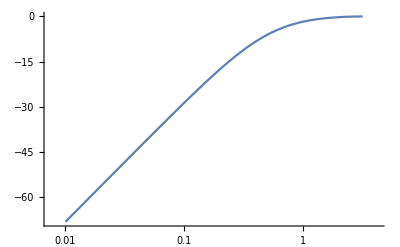

```mathematica
(* a0, a1, a2. Note a0 will be normalised to 1 so all others are divided by a0 *)
a0hp[γ_]:=γ^2+2 γ+1
a1hp[γ_]:=2 (γ^2-1)/a0hp[γ]
a2hp[γ_]:=(γ^2-2 γ+1)/a0hp[γ]
 
(* b0, b1, b2 *)
b0hp[γ_]:=1/a0hp[γ]
b1hp[γ_]:=-2/a0hp[γ]
b2hp[γ_]:=1/a0hp[γ]
    
lwHp[z_,fc_]:=(b0hp[γ[fc]] + b1hp[γ[fc]]z^(-1) + b2hp[γ[fc]]z^(-2))/(1 + a1hp[γ[fc]]z^(-1) + a2hp[γ[fc]]z^(-2))

LogLinearPlot[linearToDb[Abs[lwHp[zz[ω],0.5]]],{ω,0.01,π}]
```

Sum of lowpass and highpass transfer functions. This looks wrong.

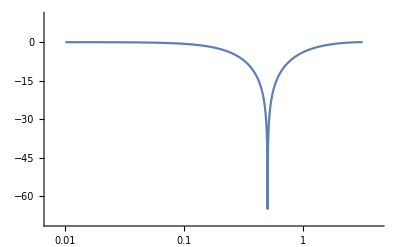

```mathematica
LogLinearPlot[linearToDb[Abs[lwHp[zz[ω],0.5]+lwLp[zz[ω],0.5]]],{ω,0.01,π}, PlotRange->{-70, 10}]
```

Difference of lowpass and highpass transfer functions. This looks correct and indicates that one of the two filters should have its b coefficients negated. I think we should negate the coefficients on the highpass filter.

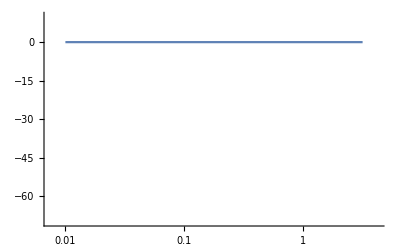

```mathematica
LogLinearPlot[linearToDb[Abs[lwLp[zz[ω],0.5]-lwHp[zz[ω],0.5]]],{ω,0.01,π}, PlotRange->{-70, 10}]
```